# Science Homework Karan Shah

My favorite 2D 3 Color Totalistic CA is Rule 709991552. The following plot shows Rule 709991552 at time step 142 with an infinite canvas and central seed.
I decided to use Georgia Tech colors. 0 -> White, 1 -> Navy Blue, 2->Gold.

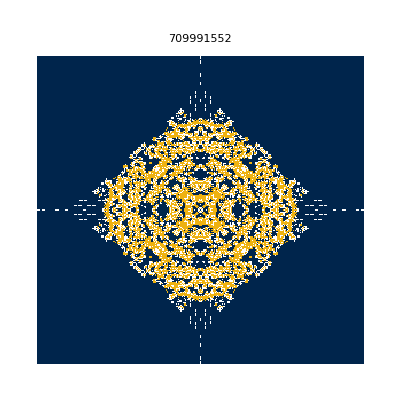

```mathematica
ArrayPlot[CellularAutomaton[
{709991552,{3,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},{{{142}},All,All}],PlotLabel->chk, ColorRules->{0->White,1->RGBColor["#00254c"],2->RGBColor["#EEB211"]}]
```

Interactive:

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[
{709991552,{3,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},{{{t}},All,All}],PlotLabel->chk, ColorRules->{0->White,1->RGBColor["#00254c"],2->RGBColor["#EEB211"]}] ,{{t,92,"Time Step"},1,150,1}]
```

There are a couple of peculiar things I noticed about it:

1) Its X Slice resembles a distorted Sierpinsky triangle (Nested triangles). The following is an XSlice plot till 50 steps.

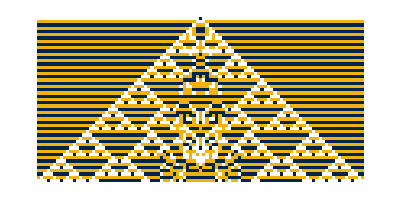

```mathematica
ArrayPlot[CellularAutomaton[
{709991552,{3,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},{50,{{0}}}],ColorRules->{0->White,1->RGBColor["#00254c"],2->RGBColor["#EEB211"]}]
```

2) As you can see from the above figure and by playing around with the simulator, the 1s and 2s are interchanged at each time step. This is apparent in the graph below (Count proportion on the Y axis, Time on the X):

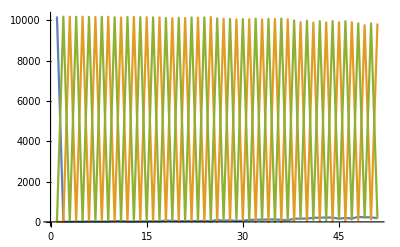

```mathematica
ListLinePlot[Transpose[Map[Function[color,Lookup[Counts[Flatten[#]],color,0]],{0,1,2}]&/@CellularAutomaton[{709991552,{3,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},50]]]
```

3) When playing with the oscillator, you will notice that period 2 oscillatory blinkers appear on the periphery of the central shape. These are the small white bars that oscillate between horizontal and vertical orientations.
(Info: https://en.wikipedia.org/wiki/Oscillator_(cellular_automaton))

```mathematica
CloudDeploy[Manipulate[ArrayPlot[CellularAutomaton[
{709991552,{3,{{1,1,1},{1,1,1},{1,1,1}}},{1,1}},{{{1}},0},{{{t}},All,All}],PlotLabel->chk, ColorRules->{0->White,1->RGBColor["#00254c"],2->RGBColor["#EEB211"]}] ,{{t,142,"Time Step"},1,150,1}] ]
```

CloudObject[]